```mathematica
ClearAll;
n=10;
H=10;

P1={{1/2,1/2},{1/2,1/2}};
(*P1={{2/3,1/3},{1/3,2/3}};*)
P2={{1/2,1/2},{1/2,1/2}};

S={1,2};
X=Range[n];
g=ConstantArray[0,{n}];
tildeq=ConstantArray[0,{n}];
For[x=1,x<=n,x++,
g[[x]]=If[x==1,2,If[Mod[x,2]==0,2,If[Mod[x,2]==1,1]]];
tildeq[[x]]=If[x==1,c/5,If[Mod[x,2]==0,(5-c)/25,If[Mod[x,2]==1,1/4]]];
]
tildeP1=ConstantArray[0,{n,n}];
tildeP2=ConstantArray[0,{n,n}];
For[y=1,y<=n,y++,
For[z=1,z<=n,z++,
tildeP1[[y,z]]=P1[[g[[y]],g[[z]]]]*tildeq[[z]];
tildeP2[[y,z]]=P2[[g[[y]],g[[z]]]]*tildeq[[z]];
]
]
tildeP=1/2*(tildeP1+tildeP2);
```

```mathematica
Clear[z,x];
tildem=ConstantArray[0,{2,2}];
For[s=1,s<3,s++,
For[a=1,a<3,a++,
tildem[[s,a]]=1/(2*n*(H-1))*Sum[Boole[g[[x]]==s]*MatrixPower[tildeP,h-1][[z,x]],{h,2,H-1},{z,1,n},{x,1,n}];
tildem[[s,a]]+=1/(2*n*(H-1))*Sum[Boole[g[[x]]==s],{x,1,n}];
]
]
tildem=Simplify[tildem]
N[tildem]
```

{{11/45,11/45},{23/90,23/90}}

{{0.244444,0.244444},{0.255556,0.255556}}

```mathematica
KL[p_,q_,L_]:=Sum[p[[i]]*Log[p[[i]]/q[[i]]],{i,1,L}];
r=ConstantArray[0,{8}];
tilder=ConstantArray[0,{8}];
Clear[i]
For[i=1,i<3,i++,
r[[2*i-1]]=(1/5)*tildem[[1,i]]*P1[[i,1]];
r[[2*i]]=(1/5)*tildem[[1,i]]*P2[[i,1]];
tilder[[2*i-1]]=(c/5)*tildem[[1,i]]*P1[[i,2]];
tilder[[2*i]]=(c/5)*tildem[[1,i]]*P2[[i,2]];
]
For[i=3,i<5,i++,
r[[2*i-1]]=tildem[[1,i-2]]*(1-P1[[i-2,1]]/5);
r[[2*i]]=tildem[[1,i-2]]*(1-P2[[i-2,1]]/5);
tilder[[2*i-1]]=tildem[[1,i-2]]*(1-c*P1[[i-2,2]]/5);
tilder[[2*i]]=tildem[[1,i-2]]*(1-c*P2[[i-2,2]]/5);
]
Divergence[C_]:=Simplify[Assuming[C<5&&C>0,
10*KL[tilder,r,8]
+(C/5)*10*(tildem[[1,1]]*KL[P1[[2,All]],P1[[1,All]],2]+tildem[[1,2]]*KL[P2[[2,All]],P2[[1,All]],2])/.{c->C}]]
Simplify[Divergence[C]]
```

44/45 (-((-10+C) Log[(10-C)/9])+C Log[C])

1.

1.02845×10^-12

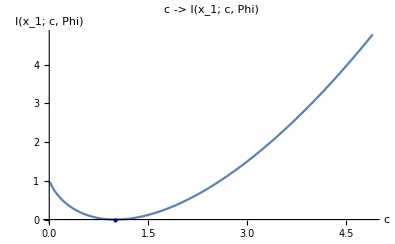

```mathematica
Coptimal=C/.Last[NMinimize[{Divergence[C],C>0&&C<5},C]]
Divergence[Coptimal]

plot=Plot[Divergence[C],{C,0.01,4.9},AxesLabel->{c,"I(x_1; c, Phi)"},PlotLabel->"c -> I(x_1; c, Phi)"];
optimal=Graphics[{PointSize[Large],Blue,Point[{Coptimal,Divergence[Coptimal]}]}];
Show[plot,optimal]
```

```mathematica
Export["/Users/nicklee/Dropbox/Markovian-data/NeurIPS 2022 Submission/figs/I=0.pdf",%71,"PDF"]
```

/Users/nicklee/Dropbox/Markovian-data/NeurIPS 2022 Submission/figs/I=0.pdf